```mathematica
x1:=1
x2:=2
x3:=3
```

```mathematica
x2
```

2

```mathematica
f[x_]:=x^3
```

```mathematica
f[x2]
```

8

```mathematica
y[x_]:=f[x1]*((x-x2)*(x-x3))/((x1-x2)*(x1-x3))+f[x2]*((x-x1)*(x-x3))/((x2-x1)*(x2-x3))+f[x3]*((x-x2)*(x-x1))/((x3-x2)*(x3-x1))
```

```mathematica
Simplify[y[x]]
```

6-11 x+6 x^2

```mathematica
D[y[x],d]
```

0

```mathematica
D[y[x],x]
```

-15/2 (-3+x)+14 (-2+x)+11/2 (-1+x)

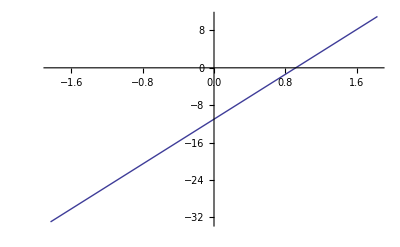

```mathematica
Plot[-15/2 (-3+x)+14 (-2+x)+11/2 (-1+x),{x,-1.8333333333333333,1.8333333333333333}]
```

```mathematica
e[x_]=f[x]-y[x]
```

-1/2 (-3+x) (-2+x)+8 (-3+x) (-1+x)-27/2 (-2+x) (-1+x)+x^3

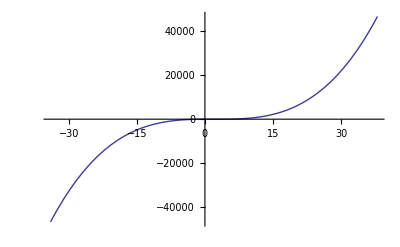

```mathematica
Plot[-1/2 (-3+x) (-2+x)+8 (-3+x) (-1+x)-27/2 (-2+x) (-1+x)+x^3,{x,-34.,38.}]
```

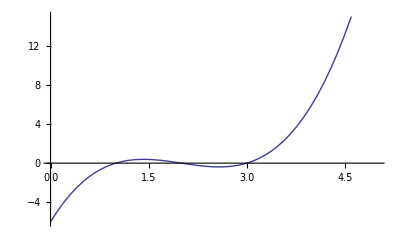

```mathematica
Plot[-1/2 (-3+x) (-2+x)+8 (-3+x) (-1+x)-27/2 (-2+x) (-1+x)+x^3,{x,0,5}]
```

```mathematica
e[x]
```

-1/2 (-3+x) (-2+x)+8 (-3+x) (-1+x)-27/2 (-2+x) (-1+x)+x^3

```mathematica
Simplify[e[x],x]
```

-6+11 True-6 True^2+True^3

```mathematica
Simplify[e[x]]
```

-6+11 x-6 x^2+x^3

```mathematica
e[x]=Simplify[e[x]]
```

-6+11 x-6 x^2+x^3

```mathematica
e[x]
```

-6+11 x-6 x^2+x^3

```mathematica
D[e[x],x]
```

11-12 x+3 x^2

```mathematica
Solve[D[e[x],x]==0,x]
```

{{x→1/3 (6-√3)},{x→1/3 (6+√3)}}

```mathematica
e[1/3 (6-√3)]
```

1/27 (6-√3)^3-1/2 (-3+1/3 (6-√3)) (-2+1/3 (6-√3))+8 (-3+1/3 (6-√3)) (-1+1/3 (6-√3))-27/2 (-2+1/3 (6-√3)) (-1+1/3 (6-√3))

```mathematica
N[1/27 (6-√3)^3-1/2 (-3+1/3 (6-√3)) (-2+1/3 (6-√3))+8 (-3+1/3 (6-√3)) (-1+1/3 (6-√3))-27/2 (-2+1/3 (6-√3)) (-1+1/3 (6-√3))]
```

0.3849

```mathematica
1/3 (6+√3)
```

1/3 (6+√3)

```mathematica
N[1/3 (6+√3)]
```

2.57735

```mathematica
1/(e[3) (6+√3)]
```

```mathematica
e[1/3 (6+√3)]
```

1/27 (6+√3)^3-1/2 (-3+1/3 (6+√3)) (-2+1/3 (6+√3))+8 (-3+1/3 (6+√3)) (-1+1/3 (6+√3))-27/2 (-2+1/3 (6+√3)) (-1+1/3 (6+√3))

```mathematica
N[1/27 (6+√3)^3-1/2 (-3+1/3 (6+√3)) (-2+1/3 (6+√3))+8 (-3+1/3 (6+√3)) (-1+1/3 (6+√3))-27/2 (-2+1/3 (6+√3)) (-1+1/3 (6+√3))]
```

-0.3849

```mathematica
e[x]
```

-6+11 x-6 x^2+x^3